# Scattering with the Fermi Pseudopotential

NPM Notes

## Single-channel problem

Let’s begin with the 3-D Schrodinger equation

(-ℏ^2/(2μ)∇^2 +V(r))Ψ(r)=E Ψ(r)

Or,

(∇^2 +k^2)Ψ(r)=(2μ)/ℏ^2 V(r)Ψ(r)

Our strategy is to turn this into an integral equation (i.e. the Lippmann-Schwinger equation). We seek the Green’s function, which is a solution to

(∇^2 +k^2)G(r,r')=δ^3(r-r')

The solution is

G(r,r')=-ⅇ^(ⅈ k |r-r'|)/(4π |r-r'|)

Note that if k^2<0, then we may wish to rewrite k^2=-κ^2 with κ^2>0, such that

G(r,r')=-ⅇ^(-κ |r-r'|)/(4π |r-r'|).

This is the form required for the bound-state problem. Note that one may obtain this form by analytic continuation, letting k become imaginary k→ ⅈ κ.

The wavefunction may then be written as

Ψ(r)=ϕ(r)+(2μ)/ℏ^2∫ⅆ^3 r'G(r,r')V(r')Ψ(r')

where ϕ(r) is a solution to the homogeneous problem (∇^2 +k^2)ϕ(r)=0.  Inserting G,

Ψ(r)=ϕ(r)-(2μ)/ℏ^2∫ⅆ^3 r' ⅇ^(ⅈ k |r-r'|)/(4π |r-r'|)V(r')Ψ(r')

Or for bound states ϕ→0 (since no bound states are supported for the homogeneous case V→0), and E<0

Ψ_b(r)=-(2μ)/ℏ^2∫ⅆ^3 r' ⅇ^(-κ |r-r'|)/(4π |r-r'|)V(r')Ψ_b(r')

We shall take V(r) to be the regularized Fermi pseudopotential:

V(r)=(4π ℏ^2 a)/(2μ)δ^3(r)∂/(∂r)(r ·)

### Bound state problem

Let us now solve the bound state problem for the eigenenergy and the wavefunction.

Ψ_b(r)=-(2μ)/ℏ^2∫ⅆ^3 r' ⅇ^(-κ |r-r'|)/(4π |r-r'|)(4π ℏ^2 a)/(2μ)δ^3(r')∂/(∂r')(r'Ψ_b(r'))

Ψ_b(r)=-a∫ⅆ^3 r' ⅇ^(-κ |r-r'|)/(|r-r'|)  δ^3(r')∂/(∂r')(r'Ψ_b(r'))

Ψ_b(r)=-a ⅇ^(-κ r)/r  (∂/(∂r')(r'Ψ_b(r')))_(r→0)

r Ψ_b(r)=-a ⅇ^(-κ r)  (∂/(∂r')(r'Ψ_b(r')))_(r'→0)

Let u(r)=r Ψ_b(r), then,

u(r)=-a ⅇ^(-κ r)  (∂/(∂r)(u(r)))_(r→0)

Evaluating at r=0

u(0)=-a   u'(0)

Which is the Bethe-Peierls boundary condition. Going back to u(r)=-a ⅇ^(-κ r)  u'(0), and taking a derivative,

u'(r)=a κ ⅇ^(-κ r)  u'(0)

evaluating at r=0

u'(0)=a κ   u'(0)

gives

κ=1/a

So,

√(-(2μ E)/ℏ^2)=1/a→ E=-ℏ^2/(2μ a^2)

and

u(r)=-a u'(0)ⅇ^(-r/a)=u(0)ⅇ^(-r/a)

u(0) must now be fixed by the normalization condition:

u(0)=1/(√(∫_0^∞ ⅆr ⅇ^(-2r/a)))=√(2/a)

u(r)=-a u'(0)ⅇ^(-r/a)=√(2/a)ⅇ^(-r/a)

### Solution for the scattering amplitude f

Now we determine the scattering amplitude.  At large r, the wavefunction in a scattering experiment will take the form

Ψ(r)=ⅇ^(ⅈ k z)+f(θ)ⅇ^(ⅈ k r)/r

Or, equivalently u(r)=r ⅇ^(ⅈ k z)+f(θ)ⅇ^(ⅈ k r)

The L-S equation reads:

Ψ(r)=ϕ(r)-(2μ)/ℏ^2∫ⅆ^3 r' ⅇ^(ⅈ k |r-r'|)/(4π |r-r'|)V(r')Ψ(r').

With the pseudopotential, and the fact that ϕ→ ⅇ^(ⅈ k z) this becomes,

Ψ(r)=ⅇ^(ⅈ k z)-(2μ)/ℏ^2∫ⅆ^3 r' ⅇ^(ⅈ k |r-r'|)/(4π |r-r'|)(4π ℏ^2 a)/(2μ)δ^3(r')∂/(∂r')(r' Ψ(r'))

Ψ(r)=ⅇ^(ⅈ k z)-a∫ⅆ^3 r' ⅇ^(ⅈ k |r-r'|)/(|r-r'|) δ^3(r')∂/(∂r')(r' Ψ(r'))

u(r)=r ⅇ^(ⅈ k z)-a ⅇ^(ⅈ k r)u'(0)

Immediately we see that

f=-a u'(0)

Again, evaluating at r=0 gives the Bethe-Peierls condition

u(0)=-a u'(0)

While taking the r-derivative leads to a formula for u'(0).  We will require the Rayliegh formula for the plane wave:

ⅇ^(ⅈ k z)=(∑_(l=0))^∞ⅈ^l(2l+1)j_l(k r)P_l(cos θ).

u'(r)=(r ⅇ^(ⅈ k z))-ⅈ k a ⅇ^(ⅈ k r)u'(0)

u'(r)=∂/(∂r)(∑_(l=0))^∞ⅈ^l(2l+1)r j_l(k r)P_l(cos θ)-a ⅈ k ⅇ^(ⅈ k r)u'(0)

Separate the l=0 term

u'(r)=∂/(∂r)(r j_0(k r))+∂/(∂r)(∑_(l=1))^∞ⅈ^l(2l+1)r j_l(k r)P_l(cos θ)-ⅈ k a ⅇ^(ⅈ k r)u'(0)

j_0(k r)=(sin k r)/(k r), so

u'(r)=(k cos(k r))/k+(∑_(l=1))^∞ⅈ^l(2l+1)∂/(∂r)(r j_l(k r))P_l(cos θ)-ⅈ k a ⅇ^(ⅈ k r)u'(0)

Now when we evaluate at r→0, ∂/(∂r)(r j_l(k r))→ 0 since r j_l(k r)∼r^(l+1) to leading order in r.

u'(0)=1-ⅈ k a u'(0)

u'(0)=1/(1+ⅈ k a)

Therefore, the scattering amplitude is

f=-a/(1+ⅈ k a)

The cross section is

ⅆσ/ⅆΩ=|f|^2=a^2/(1+(k a)^2)

σ=(4π a^2)/(1+(k a)^2)

Note that at low energy, for finite a, we have (k a)<<1

σ=(4π a^2)/(1+(k a)^2)→ 4π a^2

At unitarity, k a→∞ and the cross section is divergent at low energy:

σ≈(4π)/k^2

### Solve for the K matrix (i.e. solve for K=tan δ for only one channel)

We arrived previously at the equation

u(r)=r ⅇ^(ⅈ k z)-a ⅇ^(ⅈ k r)u'(0)

u(r)=r j_0(k r)+ (∑_(l=1))^∞ⅈ^l(2l+1)r j_l(k r)P_l(cos θ)-a ⅇ^(ⅈ k r)u'(0)

u(r)=(sin(k r))/k+ (∑_(l=1))^∞ⅈ^l(2l+1)r j_l(k r)P_l(cos θ)-a (cos(k r) +i sin(k r))u'(0)

u(r)=(1/k-i a u'(0))sin(k r)+ (∑_(l=1))^∞ⅈ^l(2l+1)r j_l(k r)P_l(cos θ)-a cos(k r)u'(0)

Note that we can again take the r-derivative and evaluate at r=0

u'(r)=(1/k-i a u'(0))k cos(k r)+ (∑_(l=1))^∞ⅈ^l(2l+1)∂/(∂r)(r j_l(k r))P_l(cos θ)+a κ sin(k r)u'(0)

u'(0)=1-i k a u'(0)

Once again giving

u'(0)=1/(1+ⅈ k a)

Therefore, now tossing out all higher partial waves,

u(r)=(1/k-i a u'(0))sin(k r)-a cos(k r)u'(0)

u(r)=(1/k-i a/(1+ⅈ k a))sin(k r)-a/(1+ⅈ k a) cos(k r)

Which, ignoring overall normalization is:

u(r)=sin(k r)-(a/(1+ⅈ k a))/(1/k-i a/(1+ⅈ k a)) cos(k r)

But this time we match to:

u(r)=f(k r)-tan δ g(k r)

where {f,g} are the (l=0) Ricatti functions. Note that this is equivalent to

u(r)→ sin (k r)+tan δ cos(k r)

because for large r,

f(k r)=√((π k r)/2)J_(1/2)(k r)→√((π k r)/2)√(2/(π k r))cos(k r - π/2) =sin(k r)

g(k r)=√((π k r)/2)Y_(1/2)(k r)→√((π k r)/2)(-1)√(2/(π k r))sin(k r-π/2)=-cos(k r) .

Comparing the two expressions for u(r) we have:

tan δ =-(a/(1+ⅈ k a))/(1/k-i a/(1+ⅈ k a))=(-k a)/(1+ⅈ k a-i k a)=-k a

tan δ =-k a

Which is indeed consistent with the effective range expansion to leading order, k cot δ=-1/a.

## Multichannel problem

Now let’s work out the multichannel problem.  The full multichannel Schrodinger equation is:

(-ℏ^2/(2μ)1∇^2 +V(r)+ϵ)Ψ(r)=E Ψ(r)

Now we let the wavefunction be a vector Ψ(r).  The matrix ϵ has only diagonal elements ϵ_i corresponding to the internal energies of the two-body system (i.e. the channel thresholds).  The potential is a matrix pseudopotential:

V(r)=(4π ℏ^2)/(2μ)A δ^3(r)∂/(∂r)(r·)

Where A is the “scattering length matrix”.  It is assumed to be symmetric, consisting of (N(N-1))/2 free parameters A_ij.  The Green’s function is a diagonal matrix with elements G_ij=G_i δ_ij,

G_i(r,r')=-ⅇ^(ⅈ k_i |r-r'|)/(4π |r-r'|)

where k_i=√((2μ (E-ϵ_i))/ℏ^2).  Note that this becomes imaginary if E<ϵ_i such that k_i→ i κ_i and in those “closed” channels, G_i(r,r')=-ⅇ^(-κ_i |r-r'|)/(4π |r-r'|).  The Lippmann-Schwinger equation becomes:

Ψ(r)=ϕ(r)+(2μ)/ℏ^2∫ⅆ^3 r'G(r,r') V(r')Ψ(r')

### Solution for the multichannel scattering amplitude

Note that since G is diagonal, the matrix G V has components: (G V)_ij=∑_k G_ik V_kj=∑_k G_i δ_ik V_kj=G_i V_ij.  Therefore (G V Ψ)_i=∑_j' G_i V_(i j')Ψ_j', corresponding to a set of coupled equations:

Ψ_i(r)=δ_ij ⅇ^(ⅈ k_j z)-(2μ)/ℏ^2∑_j' ∫ⅆ^3 r' ⅇ^(ⅈ k_i |r-r'|)/(4π |r-r'|)(4π ℏ^2)/(2μ)A_(i j')δ^3(r')∂/(∂r')(r' Ψ_j')

Ψ_i(r)=δ_ij ⅇ^(ⅈ k_j z)-∑_j' ∫ⅆ^3 r' ⅇ^(ⅈ k_i |r-r'|)/(|r-r'|)A_(i j')δ^3(r')∂/(∂r')(r' Ψ_j')

Ψ_i(r)=δ_ij ⅇ^(ⅈ k_j z)-∑_j' ⅇ^(ⅈ k_i r)/r(A_(i j')(∂/(∂r)(r Ψ_j')))_(r=0)

Ψ_i(r)=δ_ij ⅇ^(ⅈ k_j z)+[-∑_j' (A_(i j')(∂/(∂r)(r Ψ_j')))_(r=0)]ⅇ^(ⅈ k_i r)/r

Comparing to the expected form:

Ψ_i(r)=δ_ij ⅇ^(ⅈ k_j z)+f_(j→i)ⅇ^(ⅈ k_i r)/r

We have

f_(j→i)=-∑_j' (A_(i j')(∂/(∂r)(r Ψ_j')))_(r=0)

Again making the replacement r Ψ_i=u,

f_(j→i)-∑_j' A_(i j')u_j''(0)

f=-A u'(0)

Here, f is a vector with components f_i meaning f_(j→i) if i is an open channel and D_i if i is a closed channel (where the wavefunction components go as u_i=D_i ⅇ^-κ_ir. Go back to

u_i(r)=δ_ij r ⅇ^(ⅈ k_j z)-ⅇ^(ⅈ k_i r)∑_j' A_(i j')u_j''(0)

Let’s take a derivative and solve for u_i'(0).

u_i'(r)=δ_ij∂/(∂r)(r ⅇ^(ⅈ k_j z))-ⅈ k_i ⅇ^(ⅈ k_i r)∑_j' A_(i j')u_j''(0)

Using the Rayliegh formula ⅇ^(ⅈ k z)=(∑_(l=0))^∞ⅈ^l(2l+1)j_l(k r)P_l(cos θ), and separating the l=0 term, we have

∂/(∂r)(r ⅇ^(ⅈ k_j z))=∂/(∂r)(r j_0(k_j r))^(⏞^((sin(k_j r))/k_j))+(∑_(l=1))^∞ⅈ^l(2l+1)(∂/(∂r)((r j_l(k_j r))^(⏞^(∼ r^(l+1)))))^(⏞^(vanishes as r→ 0))P_l(cos θ)→^(r→0)cos(k_j r)→1

Therefore we have

u_i'(0)=δ_ij-ⅈ k_i∑_j' A_(i j')u_j''(0)

Here j="entrance channel" and i is the “exit channel”.

u_i'(0)+ⅈ k_i∑_j' A_(i j')u_j''(0)=δ_ij

∑_j' (δ_(i j')u_i'(0)+ⅈ k_i A_(i j')u_j''(0))=δ_ij

This can be written in vector form with the following definitions.  Let k be a diagonal matrix with elements ⅈ k_i.  Let d be a vector with all elements δ_ij (all elements zero unless it’s the entrance channel).  Then,

(1+k A)u'(0)=d

One could solve this numerically as a system of linear equations or formally by inverting the matrix on the left:

u'(0)=(1+k A)^-1 d

Therefore we find for f

f=-A u'(0)=-A (1+k A)^-1 d

d has elements d_i=δ_ij.  Note that this reduces to the correct 1-channel formula derived above.  It certainly seems sensible, but we’ll need to check that it behaves physically for some simple cases.

If M=-A (1+k A)^-1 then (M d)_i=∑_j' M_ij' d_j'=M_ij so a scattering amplitude matrix may also be defined simply as:

f=-A (1+k A)^-1

What does this look like for a simple 2×2 problem?

```mathematica
A=Inverse[({{1/a1, β}, {β, 1/a2}})];k=({{ⅈ √Ε, 0}, {0, -√(ϵ-Ε)}});d=({{1}, {0}});one=({{1, 0}, {0, 1}});
f=FullSimplify[-A.Inverse[(one+k.A)]];MatrixForm[f]
```

((ⅈ a1 (-1+a2 √(ϵ-Ε)))/(ⅈ-ⅈ a1 a2 β^2-ⅈ a2 √(ϵ-Ε)-a1 √Ε+a1 a2 √(ϵ-Ε) √Ε) | -(a1 a2 β)/(-1+a1 (a2 (β^2+ⅈ √(ϵ-Ε) √Ε)-ⅈ √Ε)+a2 √(ϵ-Ε))
-(a1 a2 β)/(-1+a1 (a2 (β^2+ⅈ √(ϵ-Ε) √Ε)-ⅈ √Ε)+a2 √(ϵ-Ε)) | 1/(-1/a2-(ⅈ a1 β^2)/(-ⅈ+a1 √Ε)+√(ϵ-Ε)))

First, does this make sense in the limit of no coupling?  Set β→0.

```mathematica
MatrixForm[FullSimplify[f/.β->0]]
```

((ⅈ a1)/(-ⅈ+a1 √Ε) | 0
0 | a2/(-1+a2 √(ϵ-Ε)))

This says that if channel 1 is the entrance channel, then f_(1→1)=-a_1/(1+ⅈ a_1 k), as derived earlier.  Meanwhile, if channel 2 is the entrance channel, then f_(2→2)=a_2/(-1+a_2 κ_2)=-a_2/(1+ⅈ a_2 k_2), which is exactly what it should be if channel 2 is open.  Only open channels can be entrance channels since we assume the incoming flux is of the form ⅇ^(ⅈ k z).

Now let’s see what happens if we turn on β, keeping only terms up to 𝒪(β^2):

```mathematica
fpert=FullSimplify[Normal[Series[f,{β,0,2}]]];
```

```mathematica
MatrixForm[fpert]
```

((a1 (1+(a1 a2 β^2)/(1-a2 √(ϵ-Ε))+ⅈ a1 √Ε))/(-ⅈ+a1 √Ε)^2 | (ⅈ a1 a2 β)/((-1+a2 √(ϵ-Ε)) (-ⅈ+a1 √Ε))
(ⅈ a1 a2 β)/((-1+a2 √(ϵ-Ε)) (-ⅈ+a1 √Ε)) | (-1/a2+(ⅈ a1 β^2)/(-ⅈ+a1 √Ε)+√(ϵ-Ε))/(1/a2-√(ϵ-Ε))^2)

The first term open-channel

f_(1→1)≈(a_1 (1+(a_1 a_2 β^2)/(1-a_2 √(ϵ-Ε))+ⅈ a_1 √Ε))/(-ⅈ+a_1 √Ε)^2=(ⅈ a_1)/(-ⅈ+a_1 √Ε)^2 (-ⅈ+ a_1 √Ε+(-ⅈ a_1 a_2 β^2)/(1-a_2 √(ϵ-Ε)))

f_(1→1)≈((- a_1)/(1+ⅈ a_1 k))^(⏞^(This is just the
background f_bg)) (1+ -a_2/(1-a_2 κ)-a_1/(1+ⅈ a_1 k)β^2)

```mathematica
FullSimplify[fpert[[1,1]]*fpert[[1,1]]*/.ϵ->Ε+B,{a1∈Reals,a2∈Reals,β∈Reals,Ε>0,B>0,ϵ>0,ϵ>Ε}]
```

(a1^2 (1-a2 √B+a1 a2 β^2)^2+a1^4 (-1+a2 √B)^2 Ε)/((-1+a2 √B)^2 (1+a1^2 Ε)^2)

Okay this *does* appear to have a resonance when B=1/a_2^2, as one would expect.  Let’s try to plot it for a simple case.  I’ll take:

A=(1/2 | .01
.01 | 1/2)^-1; ϵ→1;

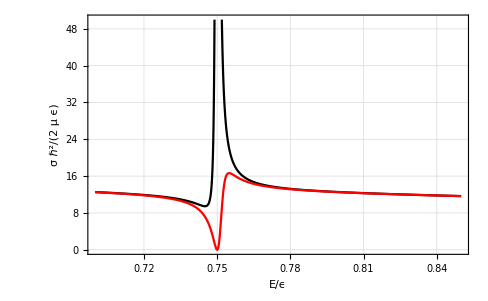

```mathematica
atest=2;Plot[{4π fpert[[1,1]]*fpert[[1,1]]*/.{a1->2,a2->atest,β->0.05,ϵ->1},
4π f[[1,1]]*f[[1,1]]*/.{a1->2,a2->atest,β->0.05,ϵ->1}},{Ε,0.7,.85},Frame->True,FrameLabel->{"Ε/ϵ","σ ℏ^2/(2  μ ϵ)"},LabelStyle->Large,GridLines->Automatic,PlotStyle->{{Black},{Red}},PlotRange->{0,50}]
```

Okay this is working exactly as expected!  I think we may have done this right!

Now what does f_(1→2) signify for the case of only channel 1 open and channel 1 the entrance channel?  Let’s go back to the LS equation:

u_i(r)=δ_ij r ⅇ^(ⅈ k_j z)-ⅇ^(ⅈ k_i r)∑_j' A_(i j')u_j''(0)=-ⅇ^-κ_ir∑_j' A_(i j')u_j''(0)

So the coefficient to the closed-channel wavefunction is:

D_i=f_(j→i)=-∑_j' A_(i j')u_j''(0)

Let’s plot |D_2|^2 for our simple problem:

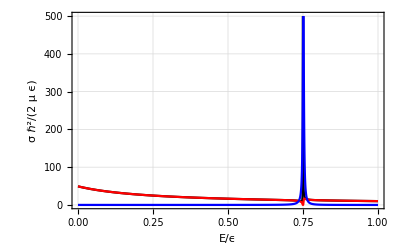

```mathematica
atest=2;Plot[{4π fpert[[1,1]]*fpert[[1,1]]*/.{a1->2,a2->atest,β->0.05,ϵ->1},
4π f[[1,1]]*f[[1,1]]*/.{a1->2,a2->atest,β->0.05,ϵ->1}, f[[1,2]]*f[[1,2]]*/.{a1->2,a2->atest,β->0.05,ϵ->1}},{Ε,0,1},Frame->True,FrameLabel->{"Ε/ϵ","σ ℏ^2/(2  μ ϵ)"},LabelStyle->Large,GridLines->Automatic,PlotStyle->{{Black},{Red},{Blue}},PlotRange->{0,500}]
```

Nice!  A large closed-channel fraction pops up right on resonance, as expected.

### The K-matrix for the multichannel problem.

Let’s now return to the LS equation and match to the following asymptotic form:

M_(i,j)→f_i δ_ij-g_i K_ij→ sin(k_i r)+K_(i j)cos(k_i r)

Where f_i,g_i satisfy the large r channel equations.

u_i(r)=δ_ij r ⅇ^(ⅈ k_j z)-ⅇ^(ⅈ k_i r)∑_j' A_(i j')u_j''(0)

Using the Rayleigh formula for the plane wave: ⅇ^(ⅈ k z)=(∑_(l=0))^∞ⅈ^l(2l+1)j_l(k r)P_l(cos θ), and the Euler formula for ⅇ^(ⅈ k_i r)

u_i(r)=δ_ij(∑_(l=0))^∞ⅈ^l(2l+1)r j_l(k_j r)P_l(cos θ)-(cos(k_i r)+ⅈ sin(k_i r))∑_j' A_(i j')u_j''(0)

u_i(r)=δ_ij((sin(k_j r))/k_j+(∑_(l=1))^∞ⅈ^l(2l+1)r j_l(k_j r)P_l(cos θ))-(cos(k_i r)+ⅈ sin(k_i r))∑_j' A_(i j')u_j''(0)

Look at only the s-wave term (you can do this rigorously by multiplying by P_0(cosθ) and integrating.  Fourier’s trick selects only l=0)

u_i(r)=δ_ij((sin(k_j r))/k_j)-(cos(k_i r)+ⅈ sin(k_i r))∑_j' A_(i j')u_j''(0)

u_i(r)=δ_ij((sin(k_j r))/k_j)-cos(k_i r)∑_j' A_(i j')u_j''(0)-ⅈ sin(k_i r)∑_j' A_(i j')u_j''(0)

u_i(r)=δ_(i j)((sin(k_j r))/k_j)-ⅈ sin(k_i r)∑_j' A_(i j')u_j''(0)-cos(k_i r)∑_j' A_(i j')u_j''(0)

Putting in the open-channel index explicitly takes u_i→M_(i j)

M_ij(r)=δ_ij((sin(k_i r))/k_i)-ⅈ sin(k_i r)∑_j' A_(i j')((∂M_(j',j))/(∂r))_0-cos(k_i r)∑_j' (A_(i j')((∂M_(j',j))/(∂r)))_0

Taking a derivative:

(∂M_ij(r))/(∂r)=δ_ij cos(k_i r)-ⅈ k_i cos(k_i r)∑_j' A_(i j')((∂M_(j',j))/(∂r))_0+k_i sin(k_i r)∑_j' (A_(i j')((∂M_(j',j))/(∂r)))_0

Evaluating at r=0

((∂M_ij)/(∂r))_0=δ_ij -ⅈ k_i∑_j' A_(i j')((∂M_(j',j))/(∂r))_0

In matrix form this says

M'(0)=1- k A M'(0)

M'(0)+ k A M'(0)=1

(1+k A) M'(0)=1

M'(0)=(1+k A)^-1

Now the solution is:

M_ij(r)=(δ_ij/k_i-(ⅈ [A M'(0)])_ij)sin(k_i r)-(cos(k_i r) [A M'(0)])_ij

M_ij(r)=sin(k_i r)-cos(k_i r)([A M'(0)]_(i j))/(δ_ij/k_i-(ⅈ [A M'(0)])_ij)

Which suggests that

K_ij=-([A M'(0)]_(i j))/(δ_ij/k_i-(ⅈ [A M'(0)])_ij)=((k_i [-A (1+k A)^-1])_(i j))/(δ_ij+ⅈ (k_i [-A (1+k A)^-1])_ij)

Recall that the scattering amplitude matrix was f=-A (1+k A)^-1

K_ij=((k_i [f])_(i j))/(δ_ij+ⅈ (k_i [f])_(i j))

Let’s see if this is consistent with the 1-channel formulas:

f=1/k ⅇ^ⅈδ sin δ

K=tan δ

This would suggest that

tan δ=(ⅇ^ⅈδ sin δ)/(1+ⅈ ⅇ^ⅈδ sin δ)

which is a true statement:

```mathematica
Simplify[ExpToTrig[(ⅇ^(ⅈ δ)Sin[δ])/(1+ⅈ ⅇ^(ⅈ δ)Sin[δ])]]
```

Tan[δ]

K_ij=((k_i [-A (1+k A)^-1])_(i j))/(δ_ij+ⅈ (k_i [-A (1+k A)^-1])_(i j))=((k_i [f])_(i j))/(δ_ij+ⅈ (k_i [f])_(i j))

What does this give for our simple 2-channel problem?

```mathematica
K11=FullSimplify[(√Ε f[[1,1]])/(1+ⅈ √Ε f[[1,1]])]
```

(a1 (1-a2 √(ϵ-Ε)) √Ε)/(-1+a1 a2 β^2+a2 √(ϵ-Ε))

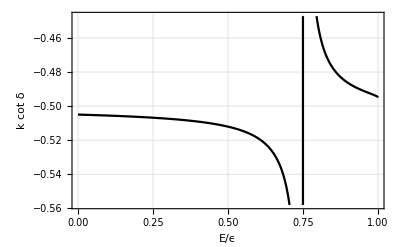

```mathematica
Plot[√Ε/K11/.{a1->2,a2->atest,β->0.05,ϵ->1},{Ε,0,1},Frame->True,FrameLabel->{"Ε/ϵ","k cot δ"},LabelStyle->Large,GridLines->Automatic,PlotStyle->Black]
```

The scattering length in the coupled system is slightly modified from its “bare” value:

```mathematica
Limit[-K11/√Ε/.{a1->2,a2->atest,β->0.05,ϵ->1},Ε->0]
```

1.9802

The effective range is twice the slope of k cot δ in the low-energy limit:

```mathematica
ERData=Table[{Ε,√Ε/K11}/.{a1->2,a2->atest,β->0.05,ϵ->1},{Ε,0.001,.1,.02}]
```

{{0.001,-0.505005},{0.021,-0.505108},{0.041,-0.505216},{0.061,-0.50533},{0.081,-0.505451}}

```mathematica
FindFit[ERData,-1/a+1/2 r0 Ε,{a,r0},Ε]
```

{a→1.98022,r0→-0.011141}

```mathematica
δ=ArcTan[K11]
```

ArcTan[(a1 (1-a2 √(ϵ-Ε)) √Ε)/(-1+a1 a2 β^2+a2 √(ϵ-Ε))]

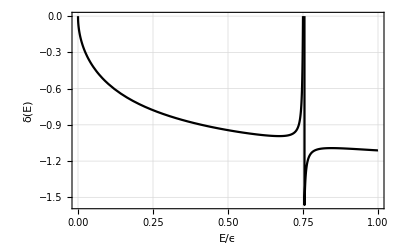

```mathematica
Plot[δ/.{a1->2,a2->atest,β->0.05,ϵ->1},{Ε,0,1},Frame->True,FrameLabel->{"Ε/ϵ","δ(Ε)"},LabelStyle->Large,GridLines->Automatic,PlotStyle->Black]
```

What about the time delay?  The time delay is:

τ=2ℏ ⅆδ/ⅆE

So if we have tanδ, then

ⅆ/ⅆE tan δ=1/(cos^2 δ)ⅆδ/ⅆE

τ/(2ℏ)=cos^2 δ (ⅆtan δ)/ⅆE=cos^2 δ (ⅆ K_11)/ⅆE

For our 2-channel problem this is pretty straight-forward:

```mathematica
τ=FullSimplify[D[ArcTan[K11],Ε]]
```

(a1 (a2^2 (a1 β^2 (ϵ-2 Ε)+(ϵ-Ε)^(3/2))-a2 (2 ϵ+a1 β^2 √(ϵ-Ε)-2 Ε)+√(ϵ-Ε)))/(2 √(ϵ-Ε) √Ε (-1-2 a1 a2 β^2 (-1+a2 √(ϵ-Ε))+2 a2 √(ϵ-Ε)+a2^2 (-ϵ+Ε)-a1^2 (Ε-2 a2 √(ϵ-Ε) Ε+a2^2 (β^4+(ϵ-Ε) Ε))))

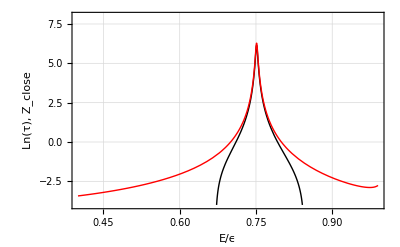

```mathematica
Plot[{Log[τ]/.{a1->2,a2->atest,β->0.05,ϵ->1},Log[(f[[1,2]]*f[[1,2]]*)/(2 √(ϵ-Ε))]/.{a1->2,a2->atest,β->0.05,ϵ->1}},{Ε,0.4,0.99},Frame->True,FrameLabel->{"Ε/ϵ","Ln(τ), Z_close"},LabelStyle->Large,GridLines->Automatic,PlotStyle->{{Black,Thin},{Red,Thin},{Blue}},PlotRange->{-4,8}]
```

In general we have: K_ij=((k_i [-A (1+k A)^-1])_(i j))/(δ_ij+ⅈ (k_i [-A (1+k A)^-1])_ij), and all energy dependence is in k_i and k.  One could in principle find a general expression, but perhaps there a better starting point for this.

Aha! one should look for the S-matrix first, and then the time delay matrix through the equation:

Q=-ⅈℏ S^-1 ⅆS/ⅆE

Since

K=-ⅈ (S-1)/(S+1)→  S =(i-K)/(ⅈ+K)

### How about going directly for the S matrix?

u_i(r)=δ_ij r ⅇ^(ⅈ k_j z)-ⅇ^(ⅈ k_i r)∑_j' A_(i j')u_j''(0)

u_i(r)=δ_ij ((sin(k_j r))/k_j+(∑_(l=1))^∞ⅈ^l(2l+1)r j_l(k_j r)P_l(cos θ))-ⅇ^(ⅈ k_i r)∑_j' A_(i j')u_j''(0)

Toss out higher partial waves l≥1 and write out the sine in terms of exponentials,

u_i(r)=δ_ij (ⅇ^(ⅈk_i r)/(2ⅈ k_j)-ⅇ^(-ⅈ k_i r)/(2ⅈ k_j))-ⅇ^(ⅈ k_i r)∑_j' A_(i j')u_j''(0)

u_i(r)=δ_ij (-ⅇ^(-ⅈ k_i r)/(2ⅈ k_i))-ⅇ^(ⅈ k_i r)(∑_j' A_(i j')u_j''(0)-δ_ij/(2ⅈ k_i))

u_i(r)=-δ_ij/(2ⅈ k_i)(ⅇ^(-ⅈ k_i r)+ⅇ^(ⅈ k_i r)(2ⅈ k_i∑_j' A_(i j')u_j''(0)-δ_ij))

```mathematica
TrigExpand[Sin[a+b]]
```

Cos[b] Sin[a]+Cos[a] Sin[b]

We compare this to the form

u_i(r)∝ⅇ^(-ⅈ k_i r)-S_ij ⅇ^(ⅈ k_i r)

S_ij=-2ⅈ k_i∑_j' A_(i j')u_j''(0)+δ_ij

So evidently

S_ij=2ⅈ k_i f_ij+δ_ij

and

f_ij=(S_ij-δ_ij)/(2ⅈ k_i)→^(see Freidrich book)(S_ij-δ_ij)/(2ⅈ √(k_i k_j))               l=0 only

Does this check out with f=1/k ⅇ^ⅈδ sinδ and S=ⅇ^(2ⅈ δ)?  yes!

S=1+2 k f

where (k)_i=ⅈ k_i

Back to the time delay matrix:

Q=-ⅈℏ S^-1 ⅆS/ⅆE=-ⅈℏ (1+2 k f)^-1(ⅆ(1+2 k f))/ⅆE

Q=-2ⅈℏ (1+2 k f)^-1(ⅆ(k f))/ⅆE

Q=-ⅈℏ2 (1-2 k [A (1+k A)^-1])^-1(ⅆ(k [-A (1+k A)^-1]))/ⅆE

Q=2ⅈℏ (1-2 k A (1+k A)^-1)^-1 ⅆ[k A (1+k A)^-1]/ⅆE

Let’s focus on the energy-derivative so we can reduce this to a form that is analytically easy to calculate:

ⅆ[k A (1+k A)^-1]/ⅆE=k A ⅆ[(1+k A)^-1]/ⅆE+ⅆk/ⅆE A (1+k A)^-1

The derivative of a matrix inverse is: (ⅆ M^-1)/ⅆE=-M^-1 ⅆM/ⅆE M^-1

ⅆ[k A (1+k A)^-1]/ⅆE=-k (A(1+k A))^-1 ⅆ[(1+k A)]/ⅆE(1+k A)^-1+ⅆk/ⅆE A (1+k A)^-1

ⅆ[k A (1+k A)^-1]/ⅆE=-k A (1+k A)^-1 ⅆk/ⅆE (A(1+k A))^-1+ⅆk/ⅆE A (1+k A)^-1

Replacing again A (1+k A)^-1→ -f

-ⅆ[k f]/ⅆE=-k f ⅆk/ⅆE f-ⅆk/ⅆE f

In fact, it’s useful to establish what the derivative of f is:

ⅆf/ⅆE=ⅆ[-A (1+k A)^-1]/ⅆE=+A (1+k A)^-1(ⅆ k)/ⅆE A (1+k A)^-1=f(ⅆ k)/ⅆE f

ⅆf/ⅆE=f(ⅆ k)/ⅆE f

With this rule, it’s easy to confirm indeed that:

Q=-2ⅈℏ (1+2 k f)^-1(ⅆ(k f))/ⅆE=-2ⅈℏ (1+2 k f)^-1(ⅆk/ⅆE f+k ⅆf/ⅆE)=-2ⅈℏ (1+2 k f)^-1(ⅆk/ⅆE f+k f(ⅆ k)/ⅆE f)

Now we can factor (ⅆ k)/ⅆE f to the right of the second factor in parentheses:

Q=-2ⅈℏ (1+2 k f)^-1(1+k f)(ⅆ k)/ⅆE f

### Test cases for more than one open channel

Next up we want to test some cases for which we have more than one open channel.  These can correspond to collisional relaxation or excitation.